# QFT compilation

## Toy device

Connectivity

```mathematica
qubitsnum=3;
```

```mathematica
Graph[Range[0,qubitsnum-1],Table[j<->j+1,{j,0,qubitsnum-2}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

-Graphics-

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->40,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->True,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.995,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{1,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.995,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{1,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->5
};
```

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

```mathematica
unitary=CalcCircuitMatrix@QFT@3;
dev=ToyDevice[];
```

```mathematica
DestroyAllQuregs[];
conf=checkedConf[dev,unitary,5];
sidelftclean={};
```

```mathematica
conf["ngatesinit"]=15;
conf["greedinessinit"]=2;
```

```mathematica
CompileCirc[conf,unitary,3,sidelftclean]
```

Compilation with automatically generated ansatz at Tue 20 Sep 2022 12:48:43

@cycle1:Tue 20 Sep 2022 12:50:07, fev:149, <E>: 0.5171976351324542 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 2, 2}

@cycle2:Tue 20 Sep 2022 12:53:43, fev:380, <E>: 0.38070096676752024 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 12, 6}

$Aborted

## Modules

```mathematica
SetAttributes[CompileCirc,HoldAll]
CompileCirc[conf_,unitary_,qubitsnum_]:=Module[{iansatz,nansatz,simpncirc,uapprox,uvc,uec,fdist},
{time,{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}}=Timing[CircuitSynthesis[qubitsnum,conf]];

iansatz=Reverse[ansatz]/.(-θvars);
nansatz=noisyAnsatz[iansatz,conf];
simpncirc=SimplifyCircuit[DeleteCases[DeleteCases[nansatz,Subscript[Depol, __][0.]],Subscript[Deph, __][0.]]];
uapprox=CalcCircuitMatrix[simpncirc];
(* fidelity distance *)
uvc=Flatten@ConjugateTranspose@unitary;
Print[Length@uapprox,Length@uvc];
uec=#.uvc&/@uapprox;
fdist=Total[Chop[#*Conjugate[#]]&/@uec]/Length@uec;
Print["compile time:",time/60," minutes; total iterations ",fev];
Print@ListPlot[Elist,AxesLabel->{"Successful iteration","Cost"}];
Print@DrawCircuit[iansatz,qubitsnum];
Print["prob(0):",probzeros];
Print["dist_fid=",fdist];
{time,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}
]
```

## Compilation : QFT3

```mathematica
QFT[nqubit_,swap_:False]:=Flatten@Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]
```

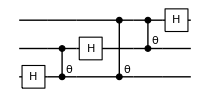

```mathematica
DrawCircuit[QFT[qubitsnum]]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
Options@ToyDevice
```

{qubitsNum→3,T1→100000,T2→40,StdPassiveNoise→True,FidSingle→0.995,EFSingle→{1,0},RabiFreq→10,FidTwo→0.995,EFTwo→{1,0},TwoGateFreq→5}

trial 1<|1→{0.400584,0.481403},2→{0.63785,0.117328},3→{0.74225,0.0363743},4→{0,0}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 01:10:14, fev:334, <E>: 0.41000946697507573 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 0, 4}

@cycle2:Fri 9 Sep 2022 01:12:38, fev:717, <E>: 0.25033543293559635 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 0, 12}

@cycle3:Fri 9 Sep 2022 01:14:25, fev:1065, <E>: 0.18379420014877787 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 38, 0, 0, 27}

@cycle4:Fri 9 Sep 2022 01:15:23, fev:1235, <E>: 0.1631880195678311 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 46, 0, 0, 28}

I'm slowing down @cycle 5

@cycle5:Fri 9 Sep 2022 01:16:19, fev:1328, <E>: 0.1631880195678311 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 46, 0, 0, 31}

I'm slowing down @cycle 6

@cycle6:Fri 9 Sep 2022 01:18:17, fev:1425, <E>: 0.1631880195678311 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 46, 0, 0, 34}

I'm slowing down @cycle 7

@cycle7:Fri 9 Sep 2022 01:23:17, fev:1530, <E>: 0.1631880195678311 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 46, 0, 0, 44}

6464

compile time:38.285 minutes; total iterations 1622

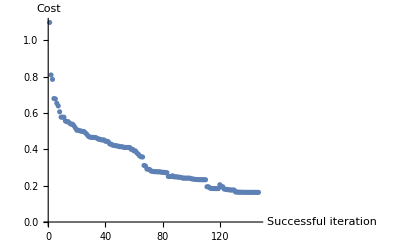

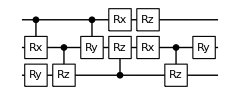

prob(0):<|0→0.331795,1→0.342206,2→0.325999|>

dist_fid=0.10741

trial 2<|1→{0.63785,0.117328},2→{0.499845,0.21725},3→{0.155551,0.0725884},4→{0.63785,0.117328}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 01:26:26, fev:290, <E>: 0.31910611593896143 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 2, 6}

@cycle2:Fri 9 Sep 2022 01:27:43, fev:450, <E>: 0.23030831880024788 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 2, 9}

I'm slowing down @cycle 3

@cycle3:Fri 9 Sep 2022 01:28:40, fev:538, <E>: 0.23030831880024788 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 2, 12}

I'm slowing down @cycle 4

@cycle4:Fri 9 Sep 2022 01:31:17, fev:617, <E>: 0.23030831880024788 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 2, 16}

I'm slowing down @cycle 5

@cycle5:Fri 9 Sep 2022 01:40:03, fev:767, <E>: 0.23030831880024788 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 2, 26}

6464

compile time:59.3542 minutes; total iterations 981

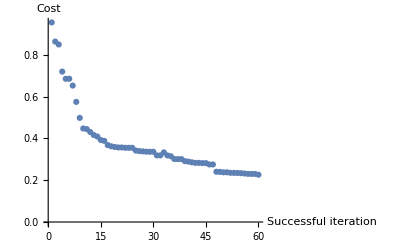

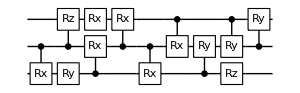

prob(0):<|0→0.333367,1→0.34206,2→0.324573|>

dist_fid=0.104765

trial 3<|1→{0,0},2→{0.74225,0.0363743},3→{0.63785,0.117328},4→{0.74225,0.0363743}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 01:44:05, fev:350, <E>: 0.35186066220182877 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 0, 5}

@cycle2:Fri 9 Sep 2022 01:47:45, fev:741, <E>: 0.2598421106137503 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 0, 8}

@cycle3:Fri 9 Sep 2022 01:49:13, fev:962, <E>: 0.1922939781968097 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 0, 12}

I'm slowing down @cycle 4

@cycle4:Fri 9 Sep 2022 01:50:08, fev:1054, <E>: 0.1922939781968097 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 0, 19}

I'm slowing down @cycle 5

@cycle5:Fri 9 Sep 2022 01:52:28, fev:1135, <E>: 0.1922939781968097 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 0, 22}

I'm slowing down @cycle 6

@cycle6:Fri 9 Sep 2022 01:57:34, fev:1230, <E>: 0.1922939781968097 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 0, 29}

6464

compile time:44.8559 minutes; total iterations 1371

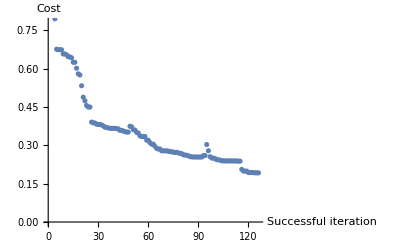

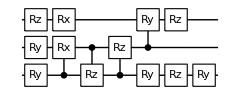

prob(0):<|0→0.31968,1→0.358246,2→0.322074|>

dist_fid=0.102145

trial 4<|1→{0,0},2→{0.499845,0.21725},3→{0.499845,0.21725},4→{0.155551,0.0725884}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 02:00:21, fev:230, <E>: 0.343141310832781 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 0, 6}

@cycle2:Fri 9 Sep 2022 02:02:16, fev:426, <E>: 0.2212930305397801 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 0, 8}

I'm slowing down @cycle 3

@cycle3:Fri 9 Sep 2022 02:04:47, fev:574, <E>: 0.2212930305397801 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 0, 8}

@cycle4:Fri 9 Sep 2022 02:13:05, fev:953, <E>: 0.18297509232502945 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 44, 0, 0, 12}

I'm slowing down @cycle 5

@cycle5:Fri 9 Sep 2022 02:16:28, fev:1069, <E>: 0.18297509232502945 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 44, 0, 0, 13}

I'm slowing down @cycle 6

@cycle6:Fri 9 Sep 2022 02:25:39, fev:1237, <E>: 0.18297509232502945 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 44, 0, 0, 17}

I'm slowing down @cycle 7

@cycle7:Fri 9 Sep 2022 02:33:21, fev:1380, <E>: 0.18297509232502945 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 44, 0, 0, 24}

6464

compile time:148.675 minutes; total iterations 1497

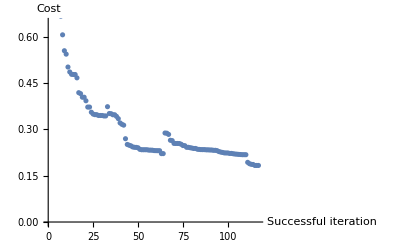

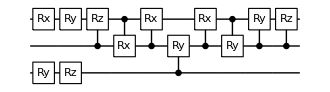

prob(0):<|0→0.338351,1→0.331919,2→0.32973|>

dist_fid=0.103943

trial 5<|1→{0.74225,0.0363743},2→{0,0},3→{0.499845,0.21725},4→{0.400584,0.481403}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 02:36:03, fev:236, <E>: 0.2969813739953787 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 0, 1}

@cycle2:Fri 9 Sep 2022 02:37:27, fev:383, <E>: 0.2665413092542495 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 0, 6}

@cycle3:Fri 9 Sep 2022 02:39:22, fev:632, <E>: 0.1865885856115554 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 36, 0, 0, 8}

I'm slowing down @cycle 4

@cycle4:Fri 9 Sep 2022 02:40:17, fev:719, <E>: 0.1865885856115554 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 36, 0, 0, 9}

I'm slowing down @cycle 5

@cycle5:Fri 9 Sep 2022 02:43:51, fev:854, <E>: 0.1865885856115554 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 36, 0, 0, 13}

I'm slowing down @cycle 6

@cycle6:Fri 9 Sep 2022 02:50:19, fev:974, <E>: 0.1865885856115554 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 36, 0, 0, 18}

6464

compile time:52.5264 minutes; total iterations 1095

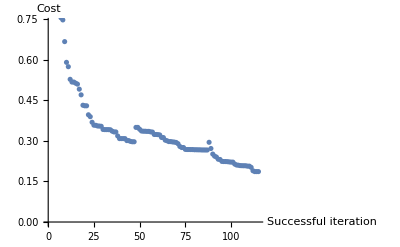

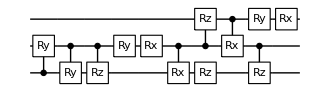

prob(0):<|0→0.319459,1→0.335759,2→0.344782|>

dist_fid=0.103684

trial 6<|1→{0,0},2→{0.63785,0.117328},3→{0.155551,0.0725884},4→{0,0}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 02:54:38, fev:425, <E>: 0.27329260531736377 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 0, 11}

@cycle2:Fri 9 Sep 2022 02:57:26, fev:708, <E>: 0.20020607562451204 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 0, 18}

I'm slowing down @cycle 3

@cycle3:Fri 9 Sep 2022 02:58:55, fev:837, <E>: 0.20020607562451204 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 0, 20}

I'm slowing down @cycle 4

@cycle4:Fri 9 Sep 2022 03:00:54, fev:904, <E>: 0.20020607562451204 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 0, 23}

I'm slowing down @cycle 5

@cycle5:Fri 9 Sep 2022 03:04:29, fev:972, <E>: 0.20020607562451204 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 0, 38}

6464

compile time:35.6811 minutes; total iterations 1091

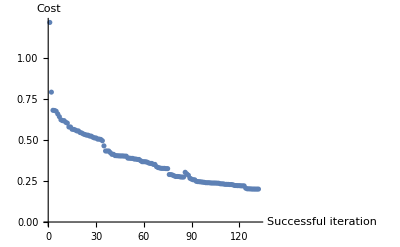

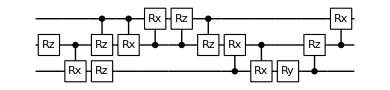

prob(0):<|0→0.329124,1→0.336162,2→0.334713|>

dist_fid=0.103056

trial 7<|1→{0.74225,0.0363743},2→{0.499845,0.21725},3→{0.74225,0.0363743},4→{0.155551,0.0725884}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 03:08:41, fev:481, <E>: 0.4144514738935254 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 1, 3}

@cycle2:Fri 9 Sep 2022 03:11:26, fev:798, <E>: 0.22003382328191712 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 23, 0, 1, 5}

@cycle3:Fri 9 Sep 2022 03:13:38, fev:1043, <E>: 0.1636364638774366 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 1, 6}

I'm slowing down @cycle 4

@cycle4:Fri 9 Sep 2022 03:14:33, fev:1113, <E>: 0.1636364638774366 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 1, 8}

I'm slowing down @cycle 5

@cycle5:Fri 9 Sep 2022 03:18:13, fev:1231, <E>: 0.1636364638774366 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 1, 16}

I'm slowing down @cycle 6

@cycle6:Fri 9 Sep 2022 03:25:21, fev:1355, <E>: 0.1636364638774366 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 1, 19}

6464

compile time:62.0652 minutes; total iterations 1588

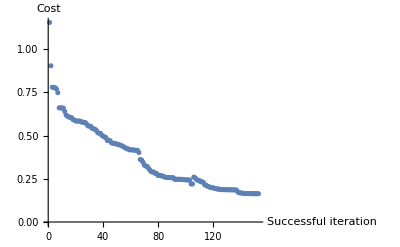

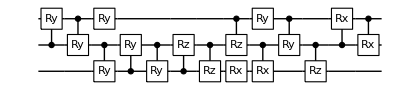

prob(0):<|0→0.334573,1→0.337511,2→0.327917|>

dist_fid=0.0992168

trial 8<|1→{0,0},2→{0.155551,0.0725884},3→{0.499845,0.21725},4→{0.499845,0.21725}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 03:30:39, fev:398, <E>: 0.21163961213865373 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 0, 9}

I'm slowing down @cycle 2

@cycle2:Fri 9 Sep 2022 03:31:37, fev:499, <E>: 0.21163961213865373 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 0, 13}

I'm slowing down @cycle 3

@cycle3:Fri 9 Sep 2022 03:33:33, fev:598, <E>: 0.21163961213865373 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 0, 26}

I'm slowing down @cycle 4

@cycle4:Fri 9 Sep 2022 03:39:31, fev:708, <E>: 0.21163961213865373 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 0, 29}

6464

compile time:38.3201 minutes; total iterations 797

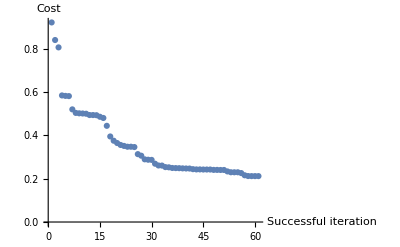

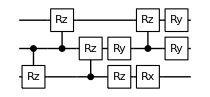

prob(0):<|0→0.319172,1→0.348946,2→0.331883|>

dist_fid=0.108169

trial 9<|1→{0.400584,0.481403},2→{0,0},3→{0.155551,0.0725884},4→{0.74225,0.0363743}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 03:42:54, fev:351, <E>: 0.19807034871982368 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 16, 0, 0, 3}

@cycle2:Fri 9 Sep 2022 03:44:02, fev:553, <E>: 0.14498411885039336 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 0, 8}

I'm slowing down @cycle 3

@cycle3:Fri 9 Sep 2022 03:44:45, fev:652, <E>: 0.14498411885039336 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 0, 14}

I'm slowing down @cycle 4

@cycle4:Fri 9 Sep 2022 03:46:15, fev:774, <E>: 0.14498411885039336 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 0, 17}

I'm slowing down @cycle 5

@cycle5:Fri 9 Sep 2022 03:54:09, fev:948, <E>: 0.14498411885039336 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 0, 19}

6464

compile time:47.2861 minutes; total iterations 1033

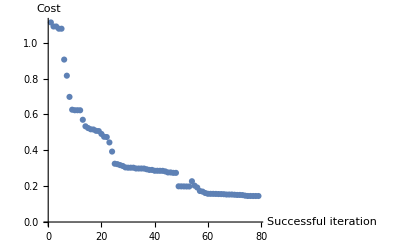

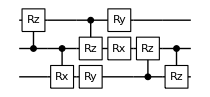

prob(0):<|0→0.329268,1→0.337643,2→0.333089|>

dist_fid=0.109707

trial 10<|1→{0.155551,0.0725884},2→{0.499845,0.21725},3→{0.63785,0.117328},4→{0.155551,0.0725884}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 03:57:12, fev:372, <E>: 0.24974209225918656 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 2, 8}

@cycle2:Fri 9 Sep 2022 03:58:06, fev:615, <E>: 0.20193147270113548 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 2, 14}

I'm slowing down @cycle 3

@cycle3:Fri 9 Sep 2022 03:58:46, fev:711, <E>: 0.20193147270113548 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 2, 17}

I'm slowing down @cycle 4

@cycle4:Fri 9 Sep 2022 04:00:41, fev:864, <E>: 0.20193147270113548 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 2, 21}

I'm slowing down @cycle 5

@cycle5:Fri 9 Sep 2022 04:06:33, fev:993, <E>: 0.20193147270113548 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 2, 27}

6464

compile time:36.1591 minutes; total iterations 1030

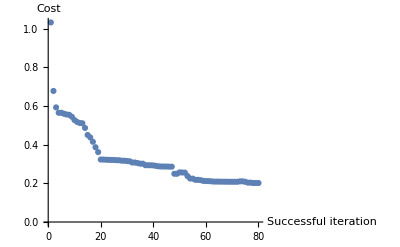

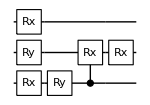

prob(0):<|0→0.343271,1→0.345494,2→0.311235|>

dist_fid=0.113269

```mathematica
qft3e05=Table[
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,4];
Print["trial ",i,varMeanInitStates[conf]];
CompileCirc[conf,unitary,qubitsnum]
,{i,10}];
```

```mathematica
DumpSave["qft3e05",qft3e05];
```

## Compilation : QFT4

```mathematica
qubitsnum=4;
Options[ToyDevice]={
qubitsNum->qubitsnum,
T1->10^5,
T2->40,
StdPassiveNoise->True,
FidSingle->0.995,
EFSingle->{1,0},
RabiFreq->10,
FidTwo->0.995,
EFTwo->{1,0},
TwoGateFreq->10
};
```

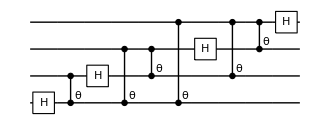

```mathematica
DrawCircuit[QFT[qubitsnum]]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
Options@ToyDevice
```

{qubitsNum→4,T1→100000,T2→40,StdPassiveNoise→True,FidSingle→0.995,EFSingle→{1,0},RabiFreq→10,FidTwo→0.995,EFTwo→{1,0},TwoGateFreq→10}

(*Test for the variety of the initial states:Here's around 7*)
Table[
conf=DefaultConfig[dev,unitary,7];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
Print[i,":",a];
{ToString[i]<>ToString[Reverse@Sort[Length/@a]]}
,{i,20}]//TableForm

1:{{0.0260508},{0.0115487},{0.0541593},{0.00511849},{0.0116821},{0.0538941,0.0538941}}

2:{{0.0487064},{0.00276653},{0.0538941},{0.0282187},{0.0260459},{0.0541593},{0.000106183}}

3:{{0,0},{0.0487064},{0.00491381},{0.0667396},{0.0541593},{0.0199868}}

4:{{0.00276653,0.00276653},{0.0181157},{0.00511849},{0.000018584,0},{0.0541593}}

5:{{0,0},{0.000106183},{0.029027},{0.012773},{0.00511849},{0.00276653}}

6:{{0.0482106,0.0482106},{0.0541593},{0.00511849},{0.0117018},{0.00583682},{0.0028228}}

7:{{0.0487064},{0.00276653,0.00276653},{0},{0.0482106},{0.000106183},{0.0115487}}

8:{{0,0.000018584,0},{0.000106183},{0.0378143},{0.0175597},{0.0028228}}

9:{{0.0028228},{0.0199868},{0.0404509},{0.00511849},{0},{0.0181157},{0.0260459}}

10:{{0.0667396},{0.0541593},{0.00276653,0.0028228,0.00276653},{0.0378143},{0.00583682}}

11:{{0.0169425},{0.0404509},{0.0378143},{0.00984488},{0,0,0}}

12:{{0.0378143},{0},{0.00511849},{0.0260459},{0.0487064,0.0487064},{0.0541593}}

13:{{0.000106183,0.000018584},{0,0},{0.0181157},{0.0378143},{0.0667396}}

14:{{0.0105271},{0},{0.00276653,0.0028228,0.0028228},{0.0260476},{0.0117018}}

15:{{0.0667396},{0.00514392,0.00511849},{0.00276653},{0.0541593},{0.0404509},{0.0487064}}

16:{{0.0254886},{0.00276653,0.00276653,0.00276653},{0.0538941},{0.00491381},{0}}

17:{{0,0},{0.0278236},{0.00276653,0.0028228},{0.00984488},{0.0487064}}

18:{{0.00583682},{0,0,0,0},{0.0538941},{0.00925872}}

19:{{0.00491381},{0.0260459},{0.000018584,0.000106183,0},{0.0169425},{0.0404509}}

20:{{0.0175597},{0.0199868},{0.0116821},{0.0260476},{0.00276653},{0.0538941},{0.0482106}}

1{2, 1, 1, 1, 1, 1}
2{1, 1, 1, 1, 1, 1, 1}
3{2, 1, 1, 1, 1, 1}
4{2, 2, 1, 1, 1}
5{2, 1, 1, 1, 1, 1}
6{2, 1, 1, 1, 1, 1}
7{2, 1, 1, 1, 1, 1}
8{3, 1, 1, 1, 1}
9{1, 1, 1, 1, 1, 1, 1}
10{3, 1, 1, 1, 1}
11{3, 1, 1, 1, 1}
12{2, 1, 1, 1, 1, 1}
13{2, 2, 1, 1, 1}
14{3, 1, 1, 1, 1}
15{2, 1, 1, 1, 1, 1}
16{3, 1, 1, 1, 1}
17{2, 2, 1, 1, 1}
18{4, 1, 1, 1}
19{3, 1, 1, 1, 1}
20{1, 1, 1, 1, 1, 1, 1}

trial 1<|1→{0.370318,0.146251},2→{0.590154,0.0156887},3→{0.0145768,0.0012749},4→{0.325692,0.149548},5→{0.370318,0.146251},6→{0.0777755,0.0362942},7→{0.371125,0.17983}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 04:30:49, fev:484, <E>: 0.4153247366448197 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 0, 10}

@cycle2:Fri 9 Sep 2022 04:43:19, fev:1006, <E>: 0.31097642189409525 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 0, 12}

@cycle3:Fri 9 Sep 2022 04:49:49, fev:1388, <E>: 0.23761142634170734 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 50, 0, 0, 12}

@cycle4:Fri 9 Sep 2022 04:55:08, fev:1659, <E>: 0.22067826070793606 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 59, 0, 0, 17}

I'm slowing down @cycle 5

@cycle5:Fri 9 Sep 2022 04:59:52, fev:1760, <E>: 0.22067826070793606 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 59, 0, 0, 23}

I'm slowing down @cycle 6

@cycle6:Fri 9 Sep 2022 05:11:12, fev:1896, <E>: 0.22067826070793606 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 59, 0, 0, 28}

I'm slowing down @cycle 7

@cycle7:Fri 9 Sep 2022 05:35:26, fev:2024, <E>: 0.22067826070793606 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 59, 0, 0, 37}

256256

compile time:282.104 minutes; total iterations 2165

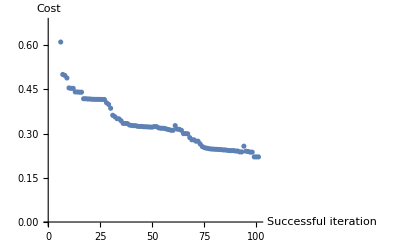

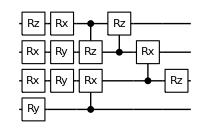

prob(0):<|0→0.235383,1→0.266139,2→0.255618,3→0.242859|>

dist_fid=0.0514824

trial 2<|1→{0.622419,0.0159647},2→{0.277011,0.136508},3→{0.382299,0.0522805},4→{0.0777755,0.0362942},5→{0,0},6→{0.277011,0.136508},7→{0.384242,0.0471466}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 06:04:11, fev:682, <E>: 0.3443619297955952 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 0, 6}

@cycle2:Fri 9 Sep 2022 06:15:39, fev:1029, <E>: 0.32172100707769113 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 0, 13}

@cycle3:Fri 9 Sep 2022 06:26:44, fev:1308, <E>: 0.2982299098778984 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 43, 0, 0, 15}

I'm slowing down @cycle 4

@cycle4:Fri 9 Sep 2022 06:32:38, fev:1432, <E>: 0.2982299098778984 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 43, 0, 0, 15}

I'm slowing down @cycle 5

@cycle5:Fri 9 Sep 2022 06:48:38, fev:1600, <E>: 0.2982299098778984 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 43, 0, 0, 19}

I'm slowing down @cycle 6

@cycle6:Fri 9 Sep 2022 07:25:21, fev:1778, <E>: 0.2982299098778984 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 43, 0, 0, 27}

256256

compile time:327.271 minutes; total iterations 1981

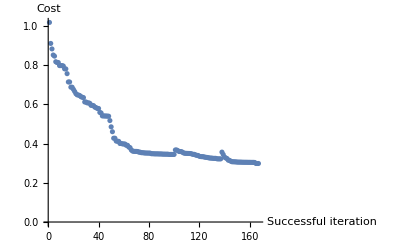

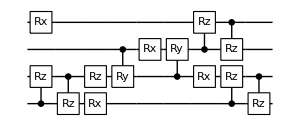

prob(0):<|0→0.237747,1→0.261111,2→0.253195,3→0.247948|>

dist_fid=0.0511282

trial 3<|1→{0.402066,0.0657661},2→{0,0},3→{0.0260596,0.00407462},4→{0.0777755,0.0362942},5→{0.0145768,0.0012749},6→{0.398367,0.0698441},7→{0.277011,0.136508}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 07:46:03, fev:570, <E>: 0.269178441312961 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 21, 0, 0, 6}

@cycle2:Fri 9 Sep 2022 07:52:37, fev:938, <E>: 0.14955800569249209 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 0, 7}

I'm slowing down @cycle 3

@cycle3:Fri 9 Sep 2022 07:54:50, fev:1022, <E>: 0.14955800569249209 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 0, 10}

I'm slowing down @cycle 4

@cycle4:Fri 9 Sep 2022 08:04:18, fev:1153, <E>: 0.14955800569249209 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 0, 17}

I'm slowing down @cycle 5

@cycle5:Fri 9 Sep 2022 08:25:49, fev:1295, <E>: 0.14955800569249209 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 0, 26}

256256

compile time:206.331 minutes; total iterations 1425

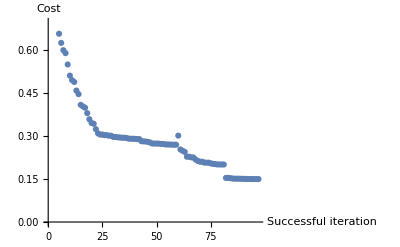

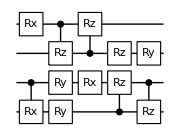

prob(0):<|0→0.244948,1→0.256593,2→0.250259,3→0.2482|>

dist_fid=0.0524071

trial 4<|1→{0.380397,0.0461617},2→{0.1476,0.034678},3→{0.139386,0.0352533},4→{0.277011,0.136508},5→{0.0777755,0.0362942},6→{0.650619,0.0179554},7→{0.318925,0.168987}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 08:48:04, fev:413, <E>: 0.43444669886830856 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 0, 7}

@cycle2:Fri 9 Sep 2022 08:57:32, fev:786, <E>: 0.36358832868689783 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 43, 0, 0, 12}

@cycle3:Fri 9 Sep 2022 09:07:50, fev:1102, <E>: 0.3310971617394896 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 58, 0, 0, 14}

@cycle4:Fri 9 Sep 2022 09:24:04, fev:1486, <E>: 0.3084976391373565 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 79, 0, 0, 18}

@cycle5:Fri 9 Sep 2022 09:31:06, fev:1785, <E>: 0.2972674688583511 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 93, 0, 0, 22}

@cycle6:Fri 9 Sep 2022 09:41:45, fev:2134, <E>: 0.2927759336953684 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 108, 0, 0, 24}

I'm slowing down @cycle 7

@cycle7:Fri 9 Sep 2022 09:46:56, fev:2239, <E>: 0.2927759336953684 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 108, 0, 0, 30}

I'm slowing down @cycle 8

@cycle8:Fri 9 Sep 2022 09:58:51, fev:2358, <E>: 0.2927759336953684 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 108, 0, 0, 36}

I'm slowing down @cycle 9

@cycle9:Fri 9 Sep 2022 10:33:05, fev:2514, <E>: 0.2927759336953684 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 108, 0, 0, 48}

256256

compile time:402.511 minutes; total iterations 2683

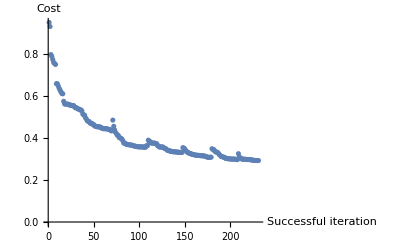

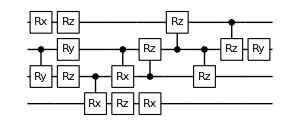

prob(0):<|0→0.249885,1→0.253805,2→0.247045,3→0.249265|>

dist_fid=0.05079

trial 5<|1→{0.370318,0.146251},2→{0.0777755,0.0362942},3→{0.380397,0.0461617},4→{0.277011,0.136508},5→{0.384242,0.0471466},6→{0.0260596,0.00407462},7→{0.318925,0.168987}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 10:55:08, fev:452, <E>: 0.3187101814145014 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 1, 4}

@cycle2:Fri 9 Sep 2022 11:02:50, fev:868, <E>: 0.2766299469872518 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 1, 8}

I'm slowing down @cycle 3

@cycle3:Fri 9 Sep 2022 11:06:34, fev:959, <E>: 0.2766299469872518 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 1, 12}

I'm slowing down @cycle 4

@cycle4:Fri 9 Sep 2022 11:16:03, fev:1061, <E>: 0.2766299469872518 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 1, 15}

I'm slowing down @cycle 5

@cycle5:Fri 9 Sep 2022 11:42:11, fev:1186, <E>: 0.2766299469872518 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 1, 19}

256256

compile time:217.605 minutes; total iterations 1310

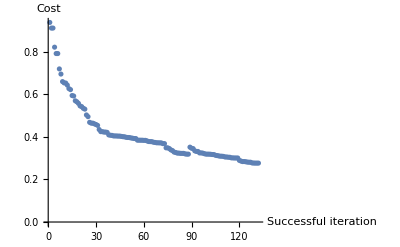

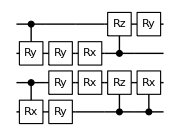

prob(0):<|0→0.232827,1→0.263624,2→0.258316,3→0.245232|>

dist_fid=0.0522131

trial 6<|1→{0.249922,0.161854},2→{0.0145768,0.0012749},3→{0.0974571,0.0283872},4→{0.651196,0.0177346},5→{0.572973,0.0204229},6→{0.249922,0.161854},7→{0.0260596,0.00407462}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 12:07:18, fev:666, <E>: 0.26657386649406617 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 18, 0, 0, 4}

I'm slowing down @cycle 2

@cycle2:Fri 9 Sep 2022 12:12:27, fev:789, <E>: 0.26657386649406617 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 18, 0, 0, 6}

I'm slowing down @cycle 3

@cycle3:Fri 9 Sep 2022 12:33:10, fev:1008, <E>: 0.26657386649406617 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 18, 0, 0, 11}

I'm slowing down @cycle 4

@cycle4:Fri 9 Sep 2022 13:07:35, fev:1174, <E>: 0.26657386649406617 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 18, 0, 0, 17}

256256

compile time:290.888 minutes; total iterations 1482

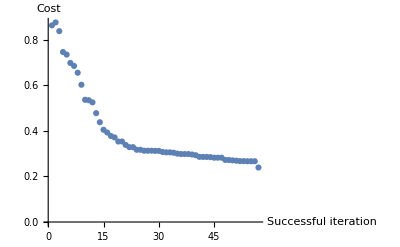

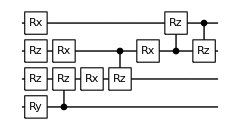

prob(0):<|0→0.242269,1→0.273678,2→0.248547,3→0.235507|>

dist_fid=0.0523064

trial 7<|1→{0.325692,0.149548},2→{0.0777755,0.0362942},3→{0,0},4→{0.325692,0.149548},5→{0.277011,0.136508},6→{0.370318,0.146251},7→{0.416475,0.0625388}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 13:25:26, fev:459, <E>: 0.5265664409919424 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 21, 0, 1, 13}

@cycle2:Fri 9 Sep 2022 13:38:41, fev:866, <E>: 0.3737866041921265 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 41, 0, 1, 17}

@cycle3:Fri 9 Sep 2022 13:45:56, fev:1205, <E>: 0.291100047549432 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 56, 0, 1, 23}

@cycle4:Fri 9 Sep 2022 13:52:40, fev:1485, <E>: 0.2796672714319439 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 71, 0, 2, 25}

@cycle5:Fri 9 Sep 2022 13:57:46, fev:1702, <E>: 0.2590346145201872 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 84, 0, 2, 30}

I'm slowing down @cycle 6

@cycle6:Fri 9 Sep 2022 14:02:12, fev:1829, <E>: 0.2590346145201872 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 84, 0, 2, 31}

I'm slowing down @cycle 7

@cycle7:Fri 9 Sep 2022 14:15:32, fev:1974, <E>: 0.2590346145201872 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 84, 0, 2, 36}

I'm slowing down @cycle 8

@cycle8:Fri 9 Sep 2022 14:45:26, fev:2134, <E>: 0.2590346145201872 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 84, 0, 2, 42}

256256

compile time:245.226 minutes; total iterations 2238

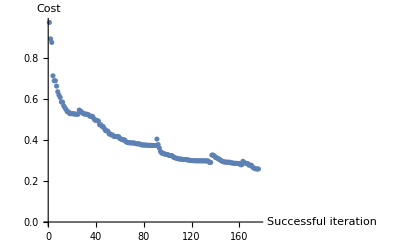

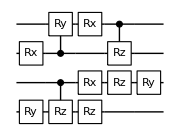

prob(0):<|0→0.242251,1→0.268843,2→0.250881,3→0.238026|>

dist_fid=0.0530265

trial 8<|1→{0.371125,0.17983},2→{0.142145,0.0361878},3→{0.622419,0.0159647},4→{0.380397,0.0461617},5→{0.433443,0.060102},6→{0.0974571,0.0283872},7→{0.650619,0.0179554}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 15:06:30, fev:494, <E>: 0.45358940268443576 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 2, 13}

@cycle2:Fri 9 Sep 2022 15:31:49, fev:1078, <E>: 0.35029103676879825 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 2, 18}

@cycle3:Fri 9 Sep 2022 15:49:57, fev:1563, <E>: 0.3177889419379915 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 43, 0, 2, 24}

I'm slowing down @cycle 4

@cycle4:Fri 9 Sep 2022 15:57:25, fev:1666, <E>: 0.3177889419379915 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 43, 0, 2, 26}

I'm slowing down @cycle 5

@cycle5:Fri 9 Sep 2022 16:15:21, fev:1820, <E>: 0.3177889419379915 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 43, 0, 2, 32}

I'm slowing down @cycle 6

@cycle6:Fri 9 Sep 2022 16:47:13, fev:1946, <E>: 0.3177889419379915 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 43, 0, 2, 34}

256256

compile time:421.257 minutes; total iterations 2922

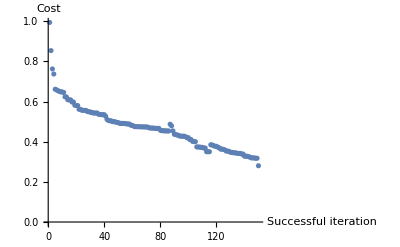

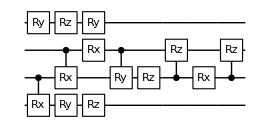

prob(0):<|0→0.236132,1→0.264151,2→0.250924,3→0.248792|>

dist_fid=0.0506826

trial 9<|1→{0.200292,0.240701},2→{0.0260596,0.00407462},3→{0.277011,0.136508},4→{0.0777755,0.0362942},5→{0.277011,0.136508},6→{0.277011,0.136508},7→{0.621828,0.0158322}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 17:25:30, fev:519, <E>: 0.3942440536224982 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 0, 3}

@cycle2:Fri 9 Sep 2022 17:37:14, fev:928, <E>: 0.2911135087463533 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 0, 9}

@cycle3:Fri 9 Sep 2022 17:48:45, fev:1299, <E>: 0.25999331184473135 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 55, 0, 0, 12}

I'm slowing down @cycle 4

@cycle4:Fri 9 Sep 2022 17:55:58, fev:1439, <E>: 0.25999331184473135 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 55, 0, 0, 14}

I'm slowing down @cycle 5

@cycle5:Fri 9 Sep 2022 18:11:59, fev:1603, <E>: 0.25999331184473135 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 55, 0, 0, 19}

I'm slowing down @cycle 6

@cycle6:Fri 9 Sep 2022 18:59:32, fev:1839, <E>: 0.25999331184473135 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 55, 0, 0, 27}

256256

compile time:380.434 minutes; total iterations 2000

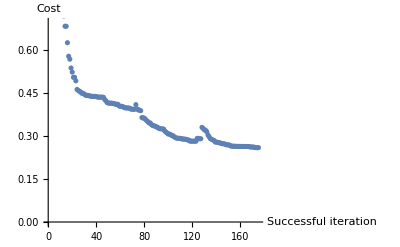

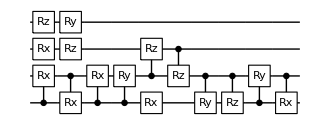

prob(0):<|0→0.230716,1→0.261883,2→0.265321,3→0.24208|>

dist_fid=0.0496239

trial 10<|1→{0.277011,0.136508},2→{0.398367,0.0698441},3→{0.371125,0.17983},4→{0.381146,0.0444515},5→{0.139386,0.0352533},6→{0.0777755,0.0362942},7→{0.139386,0.0352533}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 19:22:13, fev:408, <E>: 0.3947940010898967 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 23, 0, 2, 6}

@cycle2:Fri 9 Sep 2022 19:31:52, fev:804, <E>: 0.35320344539690873 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 44, 0, 2, 8}

@cycle3:Fri 9 Sep 2022 19:38:01, fev:1212, <E>: 0.27925725404046414 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 61, 0, 2, 13}

@cycle4:Fri 9 Sep 2022 19:43:42, fev:1487, <E>: 0.27475848442791534 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 75, 0, 2, 16}

@cycle5:Fri 9 Sep 2022 19:51:47, fev:1822, <E>: 0.26010684445338367 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 90, 0, 2, 18}

I'm slowing down @cycle 6

@cycle6:Fri 9 Sep 2022 19:57:54, fev:1939, <E>: 0.26010684445338367 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 90, 0, 2, 21}

I'm slowing down @cycle 7

@cycle7:Fri 9 Sep 2022 20:09:38, fev:2063, <E>: 0.26010684445338367 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 90, 0, 2, 29}

I'm slowing down @cycle 8

@cycle8:Fri 9 Sep 2022 20:38:55, fev:2211, <E>: 0.26010684445338367 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 90, 0, 2, 38}

256256

compile time:272.828 minutes; total iterations 2546

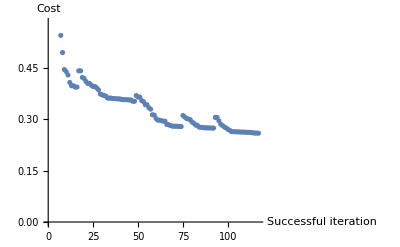

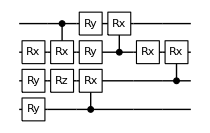

prob(0):<|0→0.228552,1→0.265964,2→0.252232,3→0.253252|>

dist_fid=0.0524376

```mathematica
qft4e05=Table[
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,7];
Print["trial ",i,varMeanInitStates[conf]];
CompileCirc[conf,unitary,qubitsnum]
,{i,10}];
```

```mathematica
DumpSave["qft4e05",qft4e05];
```

## Compilation : QFT5

```mathematica
qubitsnum=5;
Options[ToyDevice]={
qubitsNum->qubitsnum,
T1->10^5,
T2->40,
StdPassiveNoise->True,
FidSingle->0.995,
EFSingle->{1,0},
RabiFreq->10,
FidTwo->0.995,
EFTwo->{1,0},
TwoGateFreq->10
};
```

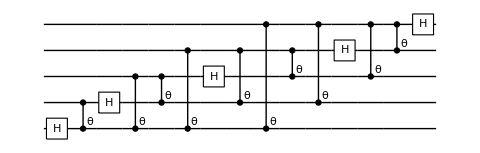

```mathematica
DrawCircuit[QFT[qubitsnum]]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
Options@ToyDevice
```

{qubitsNum→5,T1→100000,T2→40,StdPassiveNoise→True,FidSingle→0.995,EFSingle→{1,0},RabiFreq→10,FidTwo→0.995,EFTwo→{1,0},TwoGateFreq→10}

(*Test for the variety of the initial states:Here's around 15*)
Table[
conf=DefaultConfig[dev,unitary,15];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
(*Print[i,":",a];*)
{ToString[i]<>ToString[Reverse@Sort[Length/@a]]}
,{i,20}]//TableForm

1{3, 2, 2, 2, 1, 1, 1, 1, 1, 1}
2{1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
3{3, 3, 1, 1, 1, 1, 1, 1, 1, 1, 1}
4{2, 2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
5{3, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
6{3, 3, 2, 1, 1, 1, 1, 1, 1, 1}
7{3, 2, 2, 1, 1, 1, 1, 1, 1, 1, 1}
8{4, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
9{4, 2, 2, 1, 1, 1, 1, 1, 1, 1}
10{1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
11{2, 2, 2, 2, 1, 1, 1, 1, 1, 1, 1}
12{2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
13{4, 2, 1, 1, 1, 1, 1, 1, 1, 1, 1}
14{2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
15{2, 2, 2, 1, 1, 1, 1, 1, 1, 1, 1, 1}
16{2, 2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
17{4, 2, 2, 1, 1, 1, 1, 1, 1, 1}
18{2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
19{2, 2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
20{2, 2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}

trial 1<|1→{0.0885601,0.0250751},2→{0.390372,0.122857},3→{0.515827,0.0101193},4→{0.166206,0.0963007},5→{0,0},6→{0.172617,0.0926522},7→{0.339649,0.0330343},8→{0,0},9→{0.321972,0.0207679},10→{0.0878439,0.0241988},11→{0.149953,0.106575},12→{0.612341,0.0117608},13→{0.612341,0.0117608},14→{0.125093,0.0242749},15→{0.230545,0.0655637}|>

Compilation with automatically generated ansatz

@cycle1:Fri 9 Sep 2022 22:07:40, fev:406, <E>: 0.49379241542939317 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 1, 7}

@cycle2:Fri 9 Sep 2022 23:12:12, fev:754, <E>: 0.47233553025919245 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 55, 0, 1, 12}

@cycle3:Sat 10 Sep 2022 00:16:52, fev:1073, <E>: 0.43414374940851114 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 77, 0, 1, 19}

@cycle4:Sat 10 Sep 2022 01:19:22, fev:1479, <E>: 0.39045171620627506 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 99, 0, 1, 23}

I'm slowing down @cycle 5

@cycle5:Sat 10 Sep 2022 01:52:21, fev:1642, <E>: 0.39045171620627506 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 99, 0, 1, 28}

I'm slowing down @cycle 6

@cycle6:Sat 10 Sep 2022 03:12:33, fev:1826, <E>: 0.39045171620627506 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 99, 0, 1, 31}

I'm slowing down @cycle 7

@cycle7:Sat 10 Sep 2022 06:23:58, fev:2028, <E>: 0.39045171620627506 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 99, 0, 1, 59}

10241024

compile time:3325.17 minutes; total iterations 2144

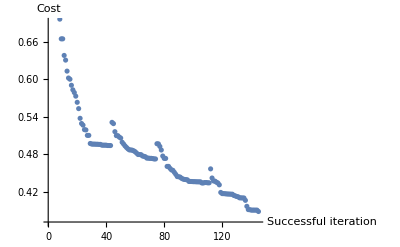

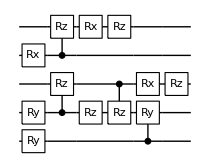

prob(0):<|0→0.186994,1→0.225146,2→0.206461,3→0.192525,4→0.188874|>

dist_fid=0.0259878

trial 2<|1→{0.337334,0.0226912},2→{0.0187684,0.00105783},3→{0.566231,0.0105742},4→{0.260607,0.0810468},5→{0.354285,0.102881},6→{0.224291,0.113203},7→{0.166937,0.0260236},8→{0.104751,0.0177782},9→{0.125093,0.0242749},10→{0.122508,0.0238073},11→{0.2306,0.0614142},12→{0.191355,0.121005},13→{0.257021,0.0690048},14→{0.373097,0.111908},15→{0.0156358,0.00244477}|>

Compilation with automatically generated ansatz

@cycle1:Sat 10 Sep 2022 08:25:29, fev:504, <E>: 0.5298238421018016 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 30, 0, 0, 14}

@cycle2:Sat 10 Sep 2022 09:26:23, fev:854, <E>: 0.4062062122053047 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 53, 0, 1, 19}

@cycle3:Sat 10 Sep 2022 10:33:24, fev:1210, <E>: 0.3603881406338921 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 76, 0, 1, 23}

@cycle4:Sat 10 Sep 2022 11:40:13, fev:1604, <E>: 0.33861370392729445 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 97, 0, 1, 28}

@cycle5:Sat 10 Sep 2022 12:29:03, fev:1922, <E>: 0.29588973989394546 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 116, 0, 2, 34}

I'm slowing down @cycle 6

@cycle6:Sat 10 Sep 2022 12:58:37, fev:2073, <E>: 0.29588973989394546 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 116, 0, 2, 40}

I'm slowing down @cycle 7

@cycle7:Sat 10 Sep 2022 14:07:25, fev:2272, <E>: 0.29588973989394546 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 116, 0, 2, 44}

I'm slowing down @cycle 8

@cycle8:Sat 10 Sep 2022 17:05:07, fev:2484, <E>: 0.29588973989394546 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 116, 0, 2, 52}

10241024

compile time:3758.19 minutes; total iterations 2601

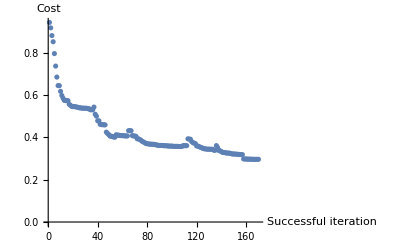

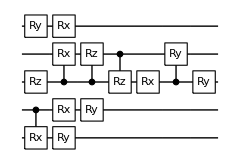

prob(0):<|0→0.18405,1→0.212307,2→0.197419,3→0.202586,4→0.203638|>

dist_fid=0.0250424

trial 3<|1→{0.232626,0.0622378},2→{0.00488227,0.000238365},3→{0.172617,0.0926522},4→{0.294724,0.0414199},5→{0.0836315,0.0247661},6→{0.198575,0.108569},7→{0.320124,0.0204044},8→{0.250403,0.0784681},9→{0.230852,0.0603445},10→{0.222191,0.11782},11→{0.51333,0.0127618},12→{0.166206,0.0963007},13→{0.0178728,0.00103619},14→{0.163653,0.0253265},15→{0.0634841,0.017193}|>

Compilation with automatically generated ansatz

@cycle1:Sat 10 Sep 2022 19:00:37, fev:516, <E>: 0.6704139582428856 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 0, 8}

@cycle2:Sat 10 Sep 2022 20:28:16, fev:929, <E>: 0.5707598276492616 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 62, 0, 0, 12}

@cycle3:Sat 10 Sep 2022 21:34:50, fev:1263, <E>: 0.49722988101218835 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 86, 0, 0, 14}

@cycle4:Sat 10 Sep 2022 22:58:53, fev:1749, <E>: 0.38977960168112147 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 107, 0, 0, 17}

@cycle5:Sat 10 Sep 2022 23:56:38, fev:2050, <E>: 0.3455615386552841 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 133, 0, 1, 23}

I'm slowing down @cycle 6

@cycle6:Sun 11 Sep 2022 00:25:17, fev:2201, <E>: 0.3455615386552841 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 133, 0, 1, 24}

I'm slowing down @cycle 7

@cycle7:Sun 11 Sep 2022 01:52:05, fev:2450, <E>: 0.3455615386552841 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 133, 0, 1, 31}

I'm slowing down @cycle 8

@cycle8:Sun 11 Sep 2022 04:36:30, fev:2648, <E>: 0.3455615386552841 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 133, 0, 1, 54}

10241024

compile time:4043.97 minutes; total iterations 2768

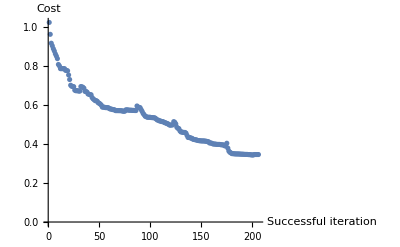

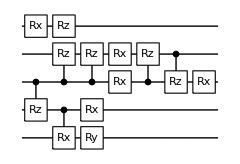

prob(0):<|0→0.178748,1→0.204099,2→0.207365,3→0.207173,4→0.202615|>

dist_fid=0.0250619

trial 4<|1→{0.354285,0.102881},2→{0,0},3→{0.163653,0.0253265},4→{0.148411,0.0227853},5→{0.222191,0.11782},6→{0.306487,0.0398995},7→{0.250403,0.0784681},8→{0.0852872,0.0254924},9→{0.107047,0.0171982},10→{0.320093,0.0230706},11→{0.00488227,0.000238365},12→{0.354539,0.0277552},13→{0.191355,0.121005},14→{0.251841,0.0459099},15→{0.148411,0.0227853}|>

Compilation with automatically generated ansatz

@cycle1:Sun 11 Sep 2022 06:31:31, fev:433, <E>: 0.452787721847708 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 0, 11}

@cycle2:Sun 11 Sep 2022 07:36:30, fev:795, <E>: 0.3832057331338435 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 44, 0, 0, 15}

@cycle3:Sun 11 Sep 2022 08:49:43, fev:1200, <E>: 0.3382767413446916 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 63, 0, 0, 16}

I'm slowing down @cycle 4

@cycle4:Sun 11 Sep 2022 09:17:19, fev:1309, <E>: 0.3382767413446916 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 63, 0, 0, 17}

I'm slowing down @cycle 5

@cycle5:Sun 11 Sep 2022 10:30:08, fev:1475, <E>: 0.3382767413446916 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 63, 0, 0, 23}

I'm slowing down @cycle 6

@cycle6:Sun 11 Sep 2022 13:44:24, fev:1667, <E>: 0.3382767413446916 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 63, 0, 0, 35}

10241024

compile time:3052.21 minutes; total iterations 1902

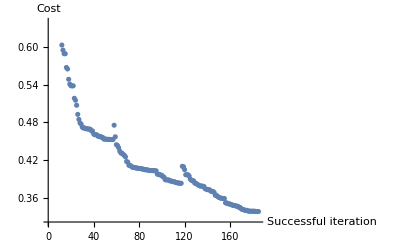

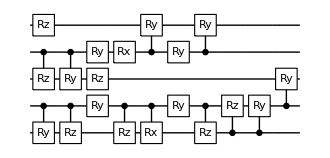

prob(0):<|0→0.199749,1→0.214539,2→0.182648,3→0.196571,4→0.206493|>

dist_fid=0.0232206

trial 5<|1→{0.32832,0.0206704},2→{0.0291668,0.00320666},3→{0.485703,0.0153282},4→{0.26418,0.0691886},5→{0.293731,0.0391475},6→{0.0852872,0.0254924},7→{0.0176759,0.00102943},8→{0.122508,0.0238073},9→{0.347491,0.0322594},10→{0.260607,0.0810468},11→{0.492005,0.0147653},12→{0.0310109,0.00323257},13→{0.0968743,0.0270354},14→{0.612798,0.0126434},15→{0.252022,0.0453697}|>

Compilation with automatically generated ansatz

@cycle1:Sun 11 Sep 2022 16:19:56, fev:611, <E>: 0.4300188765691199 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 0, 16}

@cycle2:Sun 11 Sep 2022 18:17:25, fev:1170, <E>: 0.376240734150623 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 46, 0, 0, 20}

@cycle3:Sun 11 Sep 2022 19:18:14, fev:1519, <E>: 0.36721297365336736 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 65, 0, 0, 23}

I'm slowing down @cycle 4

@cycle4:Sun 11 Sep 2022 19:56:05, fev:1679, <E>: 0.36721297365336736 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 65, 0, 0, 29}

I'm slowing down @cycle 5

@cycle5:Sun 11 Sep 2022 21:16:21, fev:1862, <E>: 0.36721297365336736 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 65, 0, 0, 31}

I'm slowing down @cycle 6

@cycle6:Mon 12 Sep 2022 01:09:48, fev:2105, <E>: 0.36721297365336736 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 65, 0, 0, 39}

10241024

compile time:3769.32 minutes; total iterations 2402

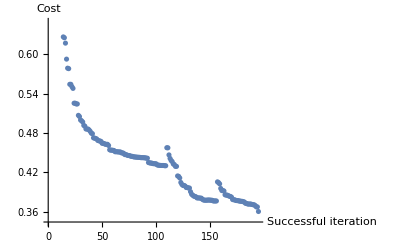

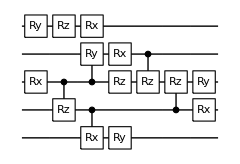

prob(0):<|0→0.191768,1→0.216879,2→0.198675,3→0.191473,4→0.201205|>

dist_fid=0.0246528

trial 6<|1→{0.262292,0.0693658},2→{0.232626,0.0622378},3→{0.0167587,0.00102737},4→{0.232626,0.0622378},5→{0.198575,0.108569},6→{0.195415,0.111369},7→{0.0196169,0.00216988},8→{0.492005,0.0147653},9→{0.35785,0.0807462},10→{0.166206,0.0963007},11→{0.130549,0.0219901},12→{0.230545,0.0655637},13→{0.0178728,0.00103619},14→{0.166206,0.0963007},15→{0.0198746,0.00110718}|>

Compilation with automatically generated ansatz

@cycle1:Mon 12 Sep 2022 03:39:32, fev:566, <E>: 0.4711712553513548 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 23, 0, 2, 7}

@cycle2:Mon 12 Sep 2022 04:42:06, fev:937, <E>: 0.413332847610223 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 43, 0, 2, 13}

@cycle3:Mon 12 Sep 2022 06:21:42, fev:1436, <E>: 0.35210342378526466 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 60, 0, 2, 23}

I'm slowing down @cycle 4

@cycle4:Mon 12 Sep 2022 07:11:52, fev:1602, <E>: 0.35210342378526466 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 60, 0, 2, 25}

I'm slowing down @cycle 5

@cycle5:Mon 12 Sep 2022 08:50:17, fev:1804, <E>: 0.35210342378526466 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 60, 0, 2, 28}

I'm slowing down @cycle 6

@cycle6:Mon 12 Sep 2022 11:52:59, fev:1971, <E>: 0.35210342378526466 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 60, 0, 2, 35}

10241024

compile time:3741.91 minutes; total iterations 2441

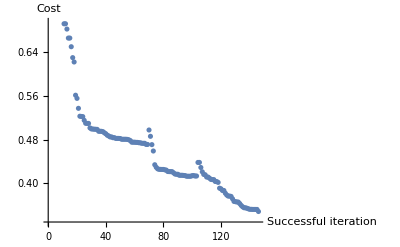

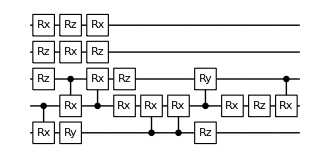

prob(0):<|0→0.184718,1→0.210324,2→0.201979,3→0.201778,4→0.201201|>

dist_fid=0.0223488

trial 7<|1→{0.120175,0.144421},2→{0.195415,0.111369},3→{0,0},4→{0.130549,0.0219901},5→{0.349228,0.0258597},6→{0.2306,0.0614142},7→{0.120111,0.0229512},8→{0.262292,0.0693658},9→{0.0333461,0.00332244},10→{0.0176759,0.00102943},11→{0.389429,0.117463},12→{0.172617,0.0926522},13→{0,0},14→{0.243218,0.0836004},15→{0.390372,0.122857}|>

Compilation with automatically generated ansatz

@cycle1:Mon 12 Sep 2022 14:36:48, fev:603, <E>: 0.508073591803287 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 0, 6}

@cycle2:Mon 12 Sep 2022 15:51:13, fev:1022, <E>: 0.3466095620206128 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 52, 0, 0, 6}

@cycle3:Mon 12 Sep 2022 16:48:34, fev:1358, <E>: 0.26669237192971984 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 69, 0, 2, 12}

I'm slowing down @cycle 4

@cycle4:Mon 12 Sep 2022 17:18:50, fev:1533, <E>: 0.26669237192971984 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 69, 0, 2, 17}

I'm slowing down @cycle 5

@cycle5:Mon 12 Sep 2022 18:29:23, fev:1747, <E>: 0.26669237192971984 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 69, 0, 2, 24}

I'm slowing down @cycle 6

@cycle6:Mon 12 Sep 2022 20:27:36, fev:1904, <E>: 0.26669237192971984 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 69, 0, 2, 41}

10241024

compile time:2829.89 minutes; total iterations 2031

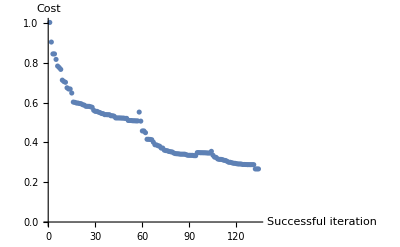

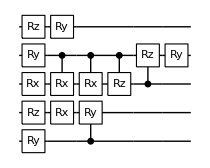

prob(0):<|0→0.185092,1→0.208784,2→0.198412,3→0.202144,4→0.205568|>

dist_fid=0.0252418

trial 8<|1→{0.32832,0.0206704},2→{0.0878439,0.0241988},3→{0.352755,0.0339115},4→{0.228238,0.0642325},5→{0.0156358,0.00244477},6→{0.104621,0.0175494},7→{0.255782,0.0686297},8→{0.532733,0.00960194},9→{0.256205,0.0680251},10→{0.00874609,0.000764941},11→{0.35785,0.0807462},12→{0.149953,0.106575},13→{0.0852872,0.0254924},14→{0.230545,0.0655637},15→{0.195415,0.111369}|>

Compilation with automatically generated ansatz

@cycle1:Mon 12 Sep 2022 22:05:47, fev:497, <E>: 0.3978819430170055 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 21, 0, 2, 11}

@cycle2:Mon 12 Sep 2022 23:18:36, fev:956, <E>: 0.32495156730686864 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 40, 0, 2, 14}

@cycle3:Tue 13 Sep 2022 00:23:23, fev:1314, <E>: 0.3124499653054103 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 64, 0, 2, 18}

I'm slowing down @cycle 4

@cycle4:Tue 13 Sep 2022 00:59:28, fev:1481, <E>: 0.3124499653054103 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 64, 0, 2, 22}

I'm slowing down @cycle 5

@cycle5:Tue 13 Sep 2022 02:02:09, fev:1649, <E>: 0.3124499653054103 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 64, 0, 2, 24}

I'm slowing down @cycle 6

@cycle6:Tue 13 Sep 2022 05:07:11, fev:1861, <E>: 0.3124499653054103 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 64, 0, 2, 37}

10241024

compile time:3036.33 minutes; total iterations 2059

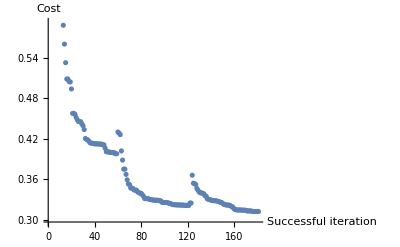

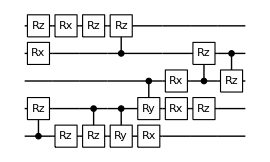

prob(0):<|0→0.183113,1→0.217863,2→0.197098,3→0.190679,4→0.211248|>

dist_fid=0.0238468

trial 9<|1→{0.259843,0.0834282},2→{0.358049,0.0810346},3→{0.163653,0.0253265},4→{0.0466653,0.0217765},5→{0.612341,0.0117608},6→{0.0878439,0.0241988},7→{0.222191,0.11782},8→{0.24124,0.0796454},9→{0.0156358,0.00244477},10→{0.0885601,0.0250751},11→{0.259843,0.0834282},12→{0.0584743,0.0183034},13→{0.353524,0.0972818},14→{0,0},15→{0.0878439,0.0241988}|>

Compilation with automatically generated ansatz

@cycle1:Tue 13 Sep 2022 07:15:36, fev:511, <E>: 0.39498908581207914 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 0, 8}

$Aborted

```mathematica
qft5e05=Table[
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,15];
Print["trial ",i,varMeanInitStates[conf]];
CompileCirc[conf,unitary,qubitsnum]
,{i,10}];
```

```mathematica
DumpSave["qft5e05",qft5e05];
```